#### Particles in a Box via DFT

a) Write down the exact energies of the first three levels of the particle in a box of length 1,
the sums of these energies for 1, 2, and 3 levels, plot the wavefunctions for each level, and plot
the densities for 1, 2, and 3 same-spin fermions in the box.

```mathematica
boxenergy[n_]:=(n^2 π^2)/2
boxenergy[1]
boxenergy[2]
boxenergy[3]
```

π^2/2

2 π^2

(9 π^2)/2

```mathematica
boxenergy[1]+boxenergy[2]
```

(5 π^2)/2

```mathematica
boxenergy[1]+boxenergy[2]+boxenergy[3]
```

7 π^2

```mathematica
wavefuncBox[n_]:=Sqrt[2]Sin[n π x]
```

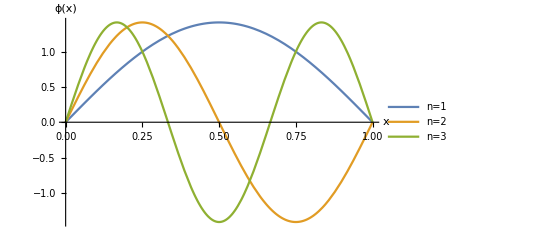

```mathematica
p1=Plot[{wavefuncBox[1],wavefuncBox[2],wavefuncBox[3]},{x,0,1},AxesLabel->{"x","ϕ(x)"},
PlotLegends->{"n=1","n=2","n=3"},PlotStyle->Thick,AxesStyle->Medium]
```

```mathematica
Export["box_wave.eps",p1];
```

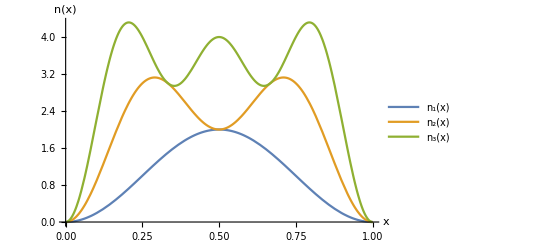

```mathematica
p2=Plot[{wavefuncBox[1]^2,wavefuncBox[1]^2+wavefuncBox[2]^2,wavefuncBox[1]^2+wavefuncBox[2]^2+wavefuncBox[3]^2},{x,0,1},AxesLabel->{"x","n(x)"},
PlotLegends->{"n_1(x)","n_2(x)","n_3(x)"},PlotStyle->Thick,AxesStyle->Medium]
```

```mathematica
Export["box_dens.eps",p2];
```

```mathematica
π^2/6.
```

1.64493

b) Solve the Euler-Lagrange equation with the TF approximation to the kinetic energy to find
the relation between N and μ. Solve for the mininimizing density, and plot it on your density
plots. Comment on the errors made by this approximate density, and how the error behaves as
N grows. Calculate the integral of n^2(x) for N = 1, 2, 3, both exactly and approximately and
comment as N grows.

```mathematica
minDens[N_]:=N
thomasKE[n_]:=π^2/6 Integrate[n^3,{x,0,1}]
```

```mathematica
tenparticles=wavefuncBox[1]^2+wavefuncBox[2]^2+wavefuncBox[3]^2+wavefuncBox[4]^2+wavefuncBox[5]^2+wavefuncBox[6]^2+wavefuncBox[7]^2+wavefuncBox[8]^2+wavefuncBox[9]^2+wavefuncBox[9]^2;
```

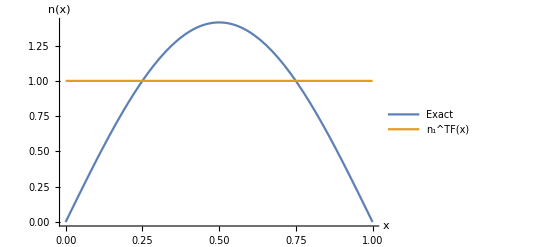

```mathematica
p3=Plot[{wavefuncBox[1],minDens[1]},{x,0,1},AxesLabel->{"x","n(x)"},
PlotLegends->{"Exact","n_1^TF(x)"},PlotStyle->Thick,AxesStyle->Medium,PlotRange->All]
```

```mathematica
Export["tf_onepart.eps",p3];
```

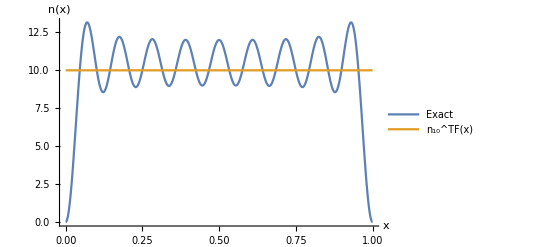

```mathematica
p4=Plot[{tenparticles,minDens[10]},{x,0,1},AxesLabel->{"x","n(x)"},
PlotLegends->{"Exact","n_10^TF(x)"},PlotStyle->Thick,AxesStyle->Medium,PlotRange->All]
```

```mathematica
Export["tf_tenpart.eps",p4];
```

```mathematica
Integrate[minDens[1]^2,{x,0,1}]
```

1

```mathematica
Integrate[minDens[2]^2,{x,0,1}]
```

4

```mathematica
Integrate[minDens[3]^2,{x,0,1}]
```

9

```mathematica
Integrate[wavefuncBox[1]^2,{x,0,1}]
```

1

```mathematica
Integrate[wavefuncBox[1]^2+wavefuncBox[2]^2,{x,0,1}]
```

2

```mathematica
Integrate[wavefuncBox[1]^2+wavefuncBox[2]^2+wavefuncBox[3]^2,{x,0,1}]
```

3

c) Make a table of the exact and approximate kinetic energies for each N and report the
percentage error. Comment on the absolute error and percent error as N grows.

```mathematica
exactT[N_]:=π^2/12 N(N+1)(2N+1)
densExactTF[N_]:=π^2/6(N^3+9/8 N^2+(3N)/8)
approxTF[N_]:=π^2/6 N^3
```

```mathematica
errorExAprrox[particle_]:=Table[{i,exactT[i]//N,approxTF[i]//N,100.*(approxTF[i]-exactT[i])/exactT[i]},{i,1,particle}]
```

```mathematica
TableForm[errorExAprrox[15],TableHeadings->{None,{"N","T^exact","T^TF_approxdens","Error (%)"}}]
```

N | T^exact | T^TF_approxdens | Error (%)
1 | 4.9348 | 1.64493 | -66.6667
2 | 24.674 | 13.1595 | -46.6667
3 | 69.0872 | 44.4132 | -35.7143
4 | 148.044 | 105.276 | -28.8889
5 | 271.414 | 205.617 | -24.2424
6 | 449.067 | 355.306 | -20.8791
7 | 690.872 | 564.212 | -18.3333
8 | 1006.7 | 842.206 | -16.3399
9 | 1406.42 | 1199.16 | -14.7368
10 | 1899.9 | 1644.93 | -13.4199
11 | 2497.01 | 2189.41 | -12.3188
12 | 3207.62 | 2842.45 | -11.3846
13 | 4041.6 | 3613.92 | -10.582
14 | 5008.82 | 4513.7 | -9.88506
15 | 6119.15 | 5551.65 | -9.27419

d) Now calculate the TF kinetic energy on the exact densities and add the results to the table,
including errors and comment as N grows. What do you conclude is the main source of error in
the self-consistent TF calculation?

```mathematica
errorExDensTF[particle_]:=Table[{i,exactT[i]//N,densExactTF[i]//N,100.*(densExactTF[i]-exactT[i])/exactT[i]},{i,1,particle}]
```

```mathematica
TableForm[errorExDensTF[15],TableHeadings->{None,{"N","T^exact","T^TF_exactdens","Error (%)"}}]
```

N | T^exact | T^TF_exactdens | Error (%)
1 | 4.9348 | 4.11234 | -16.6667
2 | 24.674 | 21.7954 | -11.6667
3 | 69.0872 | 62.9187 | -8.92857
4 | 148.044 | 137.352 | -7.22222
5 | 271.414 | 254.965 | -6.06061
6 | 449.067 | 425.627 | -5.21978
7 | 690.872 | 659.207 | -4.58333
8 | 1006.7 | 965.576 | -4.08497
9 | 1406.42 | 1354.6 | -3.68421
10 | 1899.9 | 1836.16 | -3.35498
11 | 2497.01 | 2420.11 | -3.07971
12 | 3207.62 | 3116.33 | -2.84615
13 | 4041.6 | 3934.68 | -2.6455
14 | 5008.82 | 4885.04 | -2.47126
15 | 6119.15 | 5977.28 | -2.31855

e) Remake your table to report eigenvalues, by calculating the difference between having N
and N − 1 particles in the box, and calculate errors for both self-consistent TF and TF on exact
densities.

```mathematica
scfTF[N_]:=(π^2 N^3)/6
scfdiffTF[N_]:=scfTF[N]-scfTF[N-1]//FullSimplify
diffdensExTF[N_]:=densExactTF[N]-densExactTF[N-1]//FullSimplify
diffexactT[N_]:=exactT[N]-exactT[N-1]//FullSimplify
```

```mathematica
erroreigN[particle_]:=Table[{Subscript[ϵ, i-1,i],diffexactT[i]//N,scfdiffTF[i]//N,100.*(scfdiffTF[i]-diffexactT[i])/diffexactT[i],diffdensExTF[i]//N,100.*(diffdensExTF[i]-diffexactT[i])/diffexactT[i]},{i,2,particle}]
```

```mathematica
TableForm[erroreigN[15],TableHeadings->{None,{"ϵ_(N - 1, N)","T^exact","T^(TF, scf)","Error (%)","T^TF_exactdens","Error (%)"}}]
```

ϵ_(N - 1, N) | T^exact | T^(TF, scf) | Error (%) | T^TF_exactdens | Error (%)
ϵ_(1,2) | 19.7392 | 11.5145 | -41.6667 | 17.683 | -10.4167
ϵ_(2,3) | 44.4132 | 31.2537 | -29.6296 | 41.1234 | -7.40741
ϵ_(3,4) | 78.9568 | 60.8626 | -22.9167 | 74.4333 | -5.72917
ϵ_(4,5) | 123.37 | 100.341 | -18.6667 | 117.613 | -4.66667
ϵ_(5,6) | 177.653 | 149.689 | -15.7407 | 170.662 | -3.93519
ϵ_(6,7) | 241.805 | 208.907 | -13.6054 | 233.581 | -3.40136
ϵ_(7,8) | 315.827 | 277.994 | -11.9792 | 306.369 | -2.99479
ϵ_(8,9) | 399.719 | 356.951 | -10.6996 | 389.027 | -2.6749
ϵ_(9,10) | 493.48 | 445.777 | -9.66667 | 481.554 | -2.41667
ϵ_(10,11) | 597.111 | 544.473 | -8.81543 | 583.952 | -2.20386
ϵ_(11,12) | 710.612 | 653.039 | -8.10185 | 696.218 | -2.02546
ϵ_(12,13) | 833.982 | 771.474 | -7.49507 | 818.355 | -1.87377
ϵ_(13,14) | 967.221 | 899.779 | -6.97279 | 950.361 | -1.7432
ϵ_(14,15) | 1110.33 | 1037.95 | -6.51852 | 1092.24 | -1.62963

```mathematica
π^2 N (N+1)(2N+1)/12//Expand
```

(N π^2)/12+(N^2 π^2)/4+(N^3 π^2)/6

#### Harmonic Oscillators in DFT

a) For the harmonic oscillator v(x) = x^2 /2, write the formula for the TF density in terms of
μ.

```mathematica
Integrate[Sqrt[2*(μ-x^2/2)]/π,{x,-Sqrt[2μ],Sqrt[2μ]}]
```

μ

b) By doing the integral between the turning points, find a formula for N as a function of μ.
μ = N

c) Get formulas for T_N and E_N .

```mathematica
π^2/6 Integrate[(Sqrt[2*(n-x^2/2)]/π)^3,{x,-Sqrt[2n],Sqrt[2n]}]//FullSimplify
```

n^2/4

```mathematica
Integrate[1/2 x^2 Sqrt[2*(n-x^2/2)]/π,{x,-Sqrt[2n],Sqrt[2n]}]//FullSimplify
```

n^2/4

d) By subtracting N − 1 from N , deduce a formula for the N -th energy level. What is its
error?

```mathematica
n^2/2-(n-1)^2/2//FullSimplify
```

-1/2+n

e) For N = 1, 2, 3, plot both the exact and the approximate densities of the harmonic well.
Why would the phrase ”getting the right answer for the wrong reason” come to mind?

```mathematica
densHO[n_,x_]:=Sqrt[2*(n-x^2/2)]/π
exactHOgs[x_]:=1/π^(1/4)Exp[-x^2/2]
exactHOex1[x_]:=1/π^(1/4)Sqrt[2]x Exp[-x^2/2]
exactHOex2[x_]:=Exp[-x^2/2](2 x^2-1)/(Sqrt[2] π^(1/4))
```

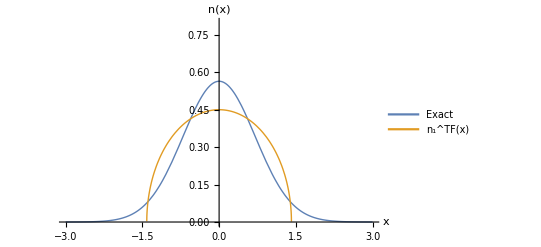

```mathematica
ho1=Plot[{exactHOgs[x]^2,densHO[1,x]},{x,-3,3},AxesLabel->{"x","n(x)"},
PlotLegends->Placed[{Style["Exact",18],Style["n_1^TF(x)",18]},{0.88,0.88}],PlotStyle->Thick,AxesStyle->Medium,PlotRange->{Automatic,{0,0.8}}]
```

```mathematica
Export["ho1_compare.eps",ho1];
```

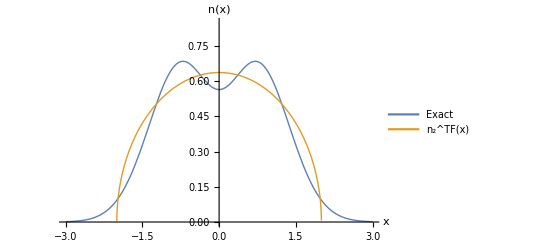

```mathematica
ho2=Plot[{exactHOgs[x]^2+exactHOex1[x]^2,densHO[2,x]},{x,-3,3},AxesLabel->{"x","n(x)"},
PlotLegends->Placed[{Style["Exact",18],Style["n_2^TF(x)",18]},{0.88,0.88}],PlotStyle->Thick,AxesStyle->Medium,PlotRange->{Automatic,{0,0.85}}]
```

```mathematica
Export["ho2_compare.eps",ho2];
```

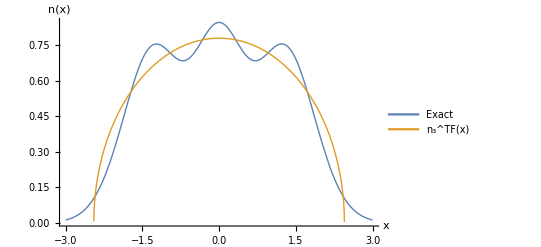

```mathematica
ho3=Plot[{exactHOgs[x]^2+exactHOex1[x]^2+exactHOex2[x]^2,densHO[3,x]},{x,-3,3},AxesLabel->{"x","n(x)"},
PlotLegends->Placed[{Style["Exact",18],Style["n_3^TF(x)",18]},{0.88,0.88}],PlotStyle->Thick,AxesStyle->Medium,PlotRange->All]
```

```mathematica
Export["ho3_compare.eps",ho3];
```

f) Calculate the integral of n^2(x) for N = 1, 2, 3 both exactly and approximately and comment
on trends of errors with N .

```mathematica
Integrate[densHO[1,x],{x,-Sqrt[2],Sqrt[2]}]
```

1

```mathematica
Integrate[densHO[2,x],{x,-Sqrt[4],Sqrt[4]}]//N
```

2.

```mathematica
Integrate[densHO[3,x],{x,-Sqrt[6],Sqrt[6]}]//N
```

3.

```mathematica
Integrate[exactHOgs[x]^2,{x,-∞,∞}]
```

1

```mathematica
Integrate[exactHOgs[x]^2+exactHOex1[x]^2,{x,-∞,∞}]
```

2

```mathematica
Integrate[exactHOgs[x]^2+exactHOex1[x]^2+exactHOex2[x]^2,{x,-∞,∞}]
```

3

#### Morse Oscillators in DFT

a) For the Morse potential given for the diatomics problem where y = N/α. Deduce a formula
for individual eigenvalues.

```mathematica
morseTF[n_,y_,v0_]:=-n v0(1-y+y^2/3)
```

```mathematica
Solve[D[morseTF[n,n/α,v0],α]==0,α]
```

{{α→(2 n)/3}}

```mathematica
morseTF[n,n/α,v0]/.{α->(2 n)/3}
```

-(n v0)/4